# Starships

## Nicki Minaj

```mathematica
-Graphics--Graphics--Graphics-
```

Starships were meant to fly...Hands up, and touch the sky.

## Intro/Verse 1

```mathematica
Clear[guitar]
```

```mathematica
guitar=Sound[{
SoundNote[{"D4","F#4","A4"},3/4x,"Guitar"],
SoundNote[{"D4","F#4","A4"},1/4x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar"],
SoundNote[{"A3","C#4","E4","A4"},3/4x,"Guitar"],
SoundNote[{"A3","C#4","E4","A4"},1/4x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar"],
SoundNote[{"B3","D4","F#4"},3/4x,"Guitar"],
SoundNote[{"B3","D4","F#4"},1/4x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar"],
SoundNote[{"F#3","A3","C#4"},3/4x,"Guitar"],
SoundNote[{"F#3","A3","C#4"},1/4x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar"],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar"]
}];
```

```mathematica
guitarCrescendo[n_,m_]:=Sound[{
SoundNote[{"D4","F#4","A4"},3/4x,"Guitar",SoundVolume->(n+1)/m],
SoundNote[{"D4","F#4","A4"},1/4x,"Guitar",SoundVolume->(n+2)/m],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar",SoundVolume->(n+4)/m],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar",SoundVolume->(n+6)/m],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar",SoundVolume->(n+8)/m],
SoundNote[{"A3","C#4","E4","A4"},3/4x,"Guitar",SoundVolume->(n+9)/m],
SoundNote[{"A3","C#4","E4","A4"},1/4x,"Guitar",SoundVolume->(n+10)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+12)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+14)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+16)/m],
SoundNote[{"B3","D4","F#4"},3/4x,"Guitar",SoundVolume->(n+17)/m],
SoundNote[{"B3","D4","F#4"},1/4x,"Guitar",SoundVolume->(n+18)/m],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar",SoundVolume->(n+20)/m],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar",SoundVolume->(n+22)/m],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar",SoundVolume->(n+24)/m],
SoundNote[{"F#3","A3","C#4"},3/4x,"Guitar",SoundVolume->(n+25)/m],
SoundNote[{"F#3","A3","C#4"},1/4x,"Guitar",SoundVolume->(n+26)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+28)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+30)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+32)/m]
}];
```

```mathematica
vocalsRap1=Sound[{
SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/4x],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["B3",1/4x,"Piano"],SoundNote["A3",1/4x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/4x],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["B3",1/4x,"Piano"],SoundNote["A3",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/4x],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["B3",1/4x,"Piano"],SoundNote["A3",1/4x,"Piano"],SoundNote["F#4",1/2x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["E4",1/2x,"Piano"],SoundNote["E4",1/2x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["F#4",1/4x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/2x,"Piano"],

SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/4x],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["B3",1/4x,"Piano"],SoundNote["A3",1/4x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/4x],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["B3",1/4x,"Piano"],SoundNote["A3",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/2x],SoundNote["F#4",1/2x,"Piano"],SoundNote[None,1/4x],SoundNote["D4",1/2x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["B3",1/4x,"Piano"],SoundNote["A3",1/4x,"Piano"],SoundNote["F#4",1/2x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["E4",1/2x,"Piano"],SoundNote["E4",1/2x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["F#4",1/4x,"Piano"],SoundNote["E4",1/4x,"Piano"],SoundNote["D4",1/4x,"Piano"],SoundNote["D4",x,"Piano"]
}];
```

```mathematica
BassDrum[n_]:=Sound[Table[SoundNote["BassDrum",x],{i,1,n}]]
SnareAlt[n_]:=Sound[Table[{SoundNote[None,x],SoundNote["Snare",x]},{i,1,n/2}]];
SnareEvery[n_]:=Sound[Table[SoundNote["Snare",x],{i,1,n}]];
HiHat[n_]:=Sound[Table[SoundNote["HiHatClosed",x],{i,1,n}]];
```

```mathematica
guitarCutTwinkle[n_,m_]:=Sound[{
SoundNote[{"D4","F#4","A4"},3/4x,"Guitar",SoundVolume->(n+1)/m],
SoundNote[{"D4","F#4","A4"},1/4x,"Guitar",SoundVolume->(n+2)/m],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar",SoundVolume->(n+4)/m],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar",SoundVolume->(n+6)/m],
SoundNote[None,1/2x],
SoundNote[{"D4","F#4","A4"},1/2x,"Guitar",SoundVolume->(n+8)/m],
SoundNote[{"A3","C#4","E4","A4"},3/4x,"Guitar",SoundVolume->(n+9)/m],
SoundNote[{"A3","C#4","E4","A4"},1/4x,"Guitar",SoundVolume->(n+10)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+12)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+14)/m],
SoundNote[None,1/2x],
SoundNote[{"G3","B3","D4","G4"},1/2x,"Guitar",SoundVolume->(n+16)/m],
SoundNote[{"B3","D4","F#4"},3/4x,"Guitar",SoundVolume->(n+17)/m],
SoundNote[{"B3","D4","F#4"},1/4x,"Guitar",SoundVolume->(n+18)/m],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar",SoundVolume->(n+20)/m],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar",SoundVolume->(n+22)/m],
SoundNote[None,1/2x],
SoundNote[{"B3","D4","F#4"},1/2x,"Guitar",SoundVolume->(n+24)/m]
}];
```

```mathematica
vocalsRap2a=Sound[{
SoundNote["F#4",1/2x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote[None,1/2x],
SoundNote["D4",1/4x,"Piano"],
SoundNote[None,1/4x],
SoundNote["C#4",1.5x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote[None,2x],

SoundNote["D4",1/2x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote[None,1/2x],
SoundNote["D4",1/4x,"Piano"],
SoundNote[None,1/4x],
SoundNote["C#4",1.5x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote[None,2x],

SoundNote["F#4",1/2x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote[None,0.75x],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["C#4",1/2x,"Piano"],
SoundNote["C#4",1/4x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",x,"Piano"],

SoundNote["F#4",1/2x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["A4",1/2x,"Piano"],
SoundNote["A4",1/2x,"Piano"],
SoundNote["B4",1/2x,"Piano"],
SoundNote["B4",1/2x,"Piano"],
SoundNote["A4",1/2x,"Piano"],
SoundNote[None,1/2x],

SoundNote["G4",1/2x,"Tinklebell"],
SoundNote["G4",1/2x,"Tinklebell"],
SoundNote["F#4",1/2x,"Tinklebell"],
SoundNote["F#4",1/2x,"Tinklebell"],
SoundNote["E4",1/2x,"Tinklebell"],
SoundNote["E4",1/2x,"Tinklebell"],
SoundNote["D4",1/2x,"Tinklebell"],

SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/4x,"Piano"]

}];
```

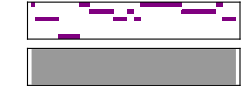

```mathematica
vocalsRap2b=Sound[{
SoundNote["F#4",1/4x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["D4",1/2x,"Piano"],
SoundNote["A3",x,"Piano"],

SoundNote["A3",1/2x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/2x,"Piano"],
SoundNote["E4",1/2x,"Piano"],
SoundNote["D4",x,"Piano"],

SoundNote["E4",1/2x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["D4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["F#4",x,"Piano"],

SoundNote["E4",1/2x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["E4",1/4x,"Piano"],
SoundNote["F#4",1/2x,"Piano"],
SoundNote["D4",x,"Piano"]

}]
```

```mathematica
15.75/0.5
```

31.5

## Prechorus

```mathematica
synth=Sound[{
SoundNote[{"D4","F#4","A4"},3/4x,"Polysynth"],SoundNote[{"D4","F#4","A4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"D4","F#4","A4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"D4","F#4","A4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"D4","F#4","A4"},1/2x,"Polysynth"],SoundNote[{"A3","C#4","E4","A4"},3/4x,"Polysynth"],SoundNote[{"A3","C#4","E4","A4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[{"B3","D4","F#4"},3/4x,"Polysynth"],SoundNote[{"B3","D4","F#4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"B3","D4","F#4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"B3","D4","F#4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"B3","D4","F#4"},1/2x,"Polysynth"],SoundNote[{"F#3","A3","C#4"},3/4x,"Polysynth"],SoundNote[{"F#3","A3","C#4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"]
}];
```

```mathematica
synthShort=Sound[{
SoundNote[{"D4","F#4","A4"},3/4x,"Polysynth"],SoundNote[{"D4","F#4","A4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"D4","F#4","A4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"D4","F#4","A4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"D4","F#4","A4"},1/2x,"Polysynth"],SoundNote[{"A3","C#4","E4","A4"},3/4x,"Polysynth"],SoundNote[{"A3","C#4","E4","A4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"G3","B3","D4","G4"},1/2x,"Polysynth"],SoundNote[{"B3","D4","F#4"},3/4x,"Polysynth"],SoundNote[{"B3","D4","F#4"},1/4x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"B3","D4","F#4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"B3","D4","F#4"},1/2x,"Polysynth"],SoundNote[None,1/2x],SoundNote[{"B3","D4","F#4"},1/2x,"Polysynth"]
}];
```

```mathematica
verseVocals=Sound[{
SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["F#5",1/2x,"ElectricPiano"],SoundNote["D5",x,"ElectricPiano"],SoundNote["F#5",1/2x,"ElectricPiano"],SoundNote["D5",x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],
SoundNote["C#5",3/4x,"ElectricPiano"],SoundNote["C#5",3/4x,"ElectricPiano"],SoundNote["B4",x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["B4",x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["B4",x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["D5",1/2x,"ElectricPiano"],SoundNote["C#5",3/4x,"ElectricPiano"],SoundNote["C#5",3/4x,"ElectricPiano"],SoundNote["D5",x,"ElectricPiano"]
}];
```

## Chorus

```mathematica
chorusVocals=Sound[{
SoundNote["F#4",x,"BrightPiano"],
SoundNote["F#4",x,"BrightPiano"],
SoundNote[None,1/2x],
SoundNote["F#4",1/2x,"BrightPiano"],
SoundNote["A4",3/4x,"BrightPiano"],
SoundNote["A4",3/4x,"BrightPiano"],
SoundNote["B4",3/2x,"BrightPiano"],
SoundNote["F#4",1/2x,"BrightPiano"],
SoundNote["E4",1/2x,"BrightPiano"],
SoundNote["D4",1/2x,"BrightPiano"],
SoundNote["B3",1/2x,"BrightPiano"],

SoundNote["F#4",x,"BrightPiano"],
SoundNote["F#4",x,"BrightPiano"],
SoundNote[None,1/2x],
SoundNote["D4",1/2x,"BrightPiano"],
SoundNote["E4",3/4x,"BrightPiano"],
SoundNote["E4",3/4x,"BrightPiano"],
SoundNote["F#4",3/2x,"BrightPiano"],
SoundNote["E4",1/2x,"BrightPiano"],
SoundNote["D4",x,"BrightPiano"],
SoundNote[None,1/2x],

SoundNote["F#4",x,"BrightPiano"],
SoundNote["F#4",x,"BrightPiano"],
SoundNote[None,1/2x],
SoundNote["F#4",1/2x,"BrightPiano"],
SoundNote["A4",3/4x,"BrightPiano"],
SoundNote["A4",3/4x,"BrightPiano"],
SoundNote["B4",3/2x,"BrightPiano"],
SoundNote["F#4",1/2x,"BrightPiano"],
SoundNote["E4",1/2x,"BrightPiano"],
SoundNote["D4",1/2x,"BrightPiano"],
SoundNote["B3",1/2x,"BrightPiano"]
}];
```

```mathematica
chorusEnd1=Sound[{SoundNote["F#4",x,"BrightPiano"],
SoundNote["F#4",x,"BrightPiano"],
SoundNote["F#4",x,"BrightPiano"],
SoundNote["E4",3/4x,"BrightPiano"],
SoundNote["E4",3/4x,"BrightPiano"],
SoundNote["D4",x,"BrightPiano"]}];
chorusEnd2=Sound[{SoundNote["F#4",x,"BrightPiano"],
SoundNote["F#4",x,"BrightPiano"]}];
```

```mathematica
chorusVocals1=Sound[{Sound[chorusVocals],Sound[chorusEnd1]}];
chorusVocals2=Sound[{Sound[chorusVocals],Sound[chorusEnd2]}];
```

```mathematica
chorusSnare1=Sound[Table[SoundNote["Snare",x],{i,1,32}]];
chorusSnare2=Sound[Table[SoundNote["Snare",x],{i,1,28}]];
```

```mathematica
chorusSynth=Sound[{
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["A5",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["A5",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["B5",1/2x,"Polysynth"],
SoundNote[None,x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote["E5",1/2x,"Polysynth"],
SoundNote["D5",1/2x,"Polysynth"],
SoundNote[None,1/2x],

SoundNote["D5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["A4",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["A4",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["B4",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["B4",1/2x,"Polysynth"],
SoundNote["D5",1/2x,"Polysynth"],
SoundNote["E5",1/2x,"Polysynth"],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],

SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["A5",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["A5",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["B5",1/2x,"Polysynth"],
SoundNote[None,x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote["E5",1/2x,"Polysynth"],
SoundNote["D5",1/2x,"Polysynth"],
SoundNote[None,1/2x],

SoundNote["D5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["F#5",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote["A4",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["A4",1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote["B4",1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"B4","B5"},1/2x,"Polysynth"],
SoundNote[{"D5","D6"},1/2x,"Polysynth"],
SoundNote[{"E5","E6"},1/2x,"Polysynth"]
}];

chorusSynthBass1=Sound[{
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"B1","B2"},x,"SynthBass"],

SoundNote[None,0.5x],
SoundNote[{"A1","A2"},1/2x,"SynthBass"],
SoundNote[{"G1","G2"},1/2x,"SynthBass"],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[{"C#1","C#2"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#1","C#2"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"D1","D2"},x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"B1","B2"},1/2x,"SynthBass"],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"B1","B2"},x,"SynthBass"],

SoundNote[None,0.5x],
SoundNote[{"A1","A2"},1/2x,"SynthBass"],
SoundNote[{"G1","G2"},1/2x,"SynthBass"],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[{"C#1","C#2"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#1","C#2"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"D1","D2"},x,"SynthBass"],
SoundNote[None,x]

}];

chorusSynthHigh=Sound[{
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"A5","A6"},1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote[{"A5","A6"},1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote[{"B5","B6"},1/2x,"Polysynth"],
SoundNote[None,x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[{"E5","E6"},1/2x,"Polysynth"],
SoundNote[{"D5","D6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],

SoundNote[{"D5","D6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"A4","A5"},1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote[{"A4","A5"},1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote[{"B4","B5"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"B4","B5"},1/2x,"Polysynth"],
SoundNote[{"D5","D6"},1/2x,"Polysynth"],
SoundNote[{"E5","E5"},1/2x,"Polysynth"],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],

SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"A5","A6"},1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote[{"A5","A6"},1/2x,"Polysynth"],
SoundNote[None,1/4x],
SoundNote[{"B5","B6"},1/2x,"Polysynth"],
SoundNote[None,x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[{"E5","E6"},1/2x,"Polysynth"],
SoundNote[{"D5","D6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"D5","D6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"],
SoundNote[None,1/2x],
SoundNote[{"F#5","F#6"},1/2x,"Polysynth"]
}];

chorusSynthBass2=Sound[{
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"B1","B2"},x,"SynthBass"],

SoundNote[None,0.5x],
SoundNote[{"A1","A2"},1/2x,"SynthBass"],
SoundNote[{"G1","G2"},1/2x,"SynthBass"],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[{"C#1","C#2"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#1","C#2"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"D1","D2"},x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"B1","B2"},1/2x,"SynthBass"],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[None,x],
SoundNote[{"D2","D3"},1/2x,"SynthBass"],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"C#2","C#3"},1/2x,"SynthBass"],
SoundNote[None,1/4x],
SoundNote[{"B1","B2"},x,"SynthBass"],

SoundNote[None,0.5x],
SoundNote[{"A1","A2"},1/2x,"SynthBass"],
SoundNote[{"G1","G2"},1/2x,"SynthBass"],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,0.5x],

SoundNote[{"F#1","F#2"},1/2x,"SynthBass"],
SoundNote[None,1/2x],
SoundNote[{"F#1","F#2"},1/2x,"SynthBass"]

}];
```

```mathematica
12.75/0.5
```

25.5

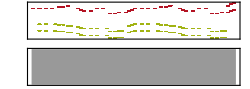

```mathematica
Sound[{Sound[chorusSynthBass1,{1x,30.5x},SoundVolume->0.5],Sound[chorusSynth,{0,32x},SoundVolume->0.5]}]
```

## Postchorus

```mathematica
higherthanaMF=Sound[{
SoundNote["D4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["D#4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["D#4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["E4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["E4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["F4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["F4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["F#4",0.25x,"Shakuhachi"],
SoundNote[None,0.25x],
SoundNote["B3",0.5x,"Shakuhachi"]
}];

breakDown=Sound[{
SoundNote[{"D4","A4","D5"},0.875x,"Square",SoundVolume->0.6],
SoundNote[{"B3","F#4","B4"},0.625x,"Square",SoundVolume->0.6],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[None,0.5x],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[None,0.5x],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[{"D4","A4","D5"},0.875x,"Square",SoundVolume->0.6],
SoundNote[{"B3","F#4","B4"},0.625x,"Square",SoundVolume->0.6],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[None,0.5x],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[None,0.5x],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[{"D4","A4","D5"},0.875x,"Square",SoundVolume->0.6],
SoundNote[{"B3","F#4","B4"},0.625x,"Square",SoundVolume->0.6],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[None,0.5x],
SoundNote["B3",0.5x,"OrchestraHit"],
SoundNote[None,0.5x],
SoundNote["B3",0.5x,"OrchestraHit"]
}];
```

## Song

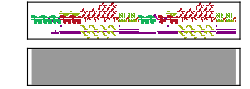

```mathematica
x=0.48;
b=0x;
Sound[{
(* Intro w/ Rap *)
Sound[guitar,{0x+b,16x+b},SoundVolume->0.5],

(* Verse 1 *)
Sound[guitar,{16x+b,32x+b},SoundVolume->0.5],Sound[vocalsRap,{14.5x+b,47.5x+b},SoundVolume->0.6],
Sound[guitar,{32x+b,48x+b},SoundVolume->0.5],Sound[BassDrum[12],{32x+b,44x+b}],
SoundNote["Clap",{38.5x+b,39x+b},SoundVolume->0.3],SoundNote["Clap",{39x+b,39.5x+b},SoundVolume->0.3],
SoundNote["Snare",{46x+b,46.75x+b},SoundVolume->0.4],SoundNote["Snare",{46.75x+b,47x+b},SoundVolume->0.4],SoundNote["Snare",{47x+b,47.25x+b},SoundVolume->0.4],

(* Prechorus 1 *)
SoundNote["CrashCymbal",{48x+b,48.5x+b},SoundVolume->0.5],
Sound[synth,{48x+b,64x+b},SoundVolume->0.5],Sound[verseVocals,{46.5x+b,62.5x+b},SoundVolume->0.8],Sound[BassDrum[16],{48x+b,64x+b}],Sound[SnareAlt[16],{48x+b,64x+b},SoundVolume->0.4],
Sound[synth,{64x+b,80x+b},SoundVolume->0.5],Sound[verseVocals,{62.5x+b,78.5x+b},SoundVolume->0.8],Sound[BassDrum[16],{64x+b,80x+b}],Sound[SnareAlt[16],{64x+b,80x+b},SoundVolume->0.4],

(* Chorus 1 *)
Sound[chorusVocals1,{81x+b,110.5x+b},SoundVolume->0.8],Sound[SnareEvery[32],{80x+b,112x+b},SoundVolume->0.4],Sound[chorusSynth,{80x+b,112x+b},SoundVolume->0.4],
Sound[chorusSynthBass1,{81x+b,110.5x+b},SoundVolume->0.5],

Sound[chorusVocals2,{113x+b,139x+b},SoundVolume->0.8],
Sound[SnareEvery[16],{112x+b,128x+b},SoundVolume->0.4],
Sound[SnareEvery[16],{128x+b,136x+b},SoundVolume->0.4],
Sound[SnareEvery[16],{136x+b,140x+b},SoundVolume->0.4],
Sound[chorusSynthHigh,{112x+b,139.5x+b},SoundVolume->0.4],
Sound[chorusSynthBass2,{113x+b,138.5x+b},SoundVolume->0.5],

Sound[higherthanaMF,{139.5x+b,144x+b},SoundVolume->0.6],
SoundNote["Snare",{142x+b,142.75x+b},SoundVolume->0.4],SoundNote["Snare",{142.75x+b,143x+b},SoundVolume->0.4],SoundNote["Snare",{143x+b,143.25x+b},SoundVolume->0.4],

(* Postchorus 1 *)
SoundNote["CrashCymbal",{144x+b,144.5x+b},SoundVolume->0.5],
Sound[breakDown,{144x+b,156x+b}],
Sound[HiHat[16],{144x+b,160x+b},SoundVolume->0.6],
Sound[BassDrum[16],{144x+b,160x+b}],Sound[SnareAlt[16],{144x+b,160x+b},SoundVolume->0.4],
Sound[higherthanaMF,{155.5x+b,160x+b},SoundVolume->0.6],

Sound[breakDown,{160x+b,172x+b}],
Sound[HiHat[16],{160x+b,176x+b},SoundVolume->0.6],
Sound[BassDrum[16],{160x+b,176x+b}],Sound[SnareAlt[16],{160x+b,176x+b},SoundVolume->0.4],
Sound[higherthanaMF,{171.5x+b,176x+b},SoundVolume->0.6],

(* Verse 2 *)
Sound[vocalsRap2a,{176x+b,208x+b}],
Sound[guitarCrescendo[32,80],{176x+b,192x+b}],Sound[BassDrum[16],{176x+b,192x+b}],
Sound[guitarCutTwinkle[64,80],{192x+b,204x+b}],Sound[BassDrum[12],{192x+b,204x+b}],
SoundNote["Snare",{207x+b,207.5x+b},SoundVolume->0.4],SoundNote["Snare",{207.5x+b,207.75x+b},SoundVolume->0.4],SoundNote["Snare",{207.75x+b,208x+b},SoundVolume->0.4],

Sound[vocalsRap2b,{208x+b,223x+b}],Sound[synthShort,{208x+b,220x+b},SoundVolume->0.5],Sound[BassDrum[16],{208x+b,224x+b}],Sound[SnareAlt[16],{208x+b,224x+b},SoundVolume->0.4],

(* Prechorus 2 *)
SoundNote["CrashCymbal",{224x+b,224.5x+b},SoundVolume->0.5],
Sound[synth,{224x+b,240x+b},SoundVolume->0.5],Sound[verseVocals,{222.5x+b,238.5x+b},SoundVolume->0.8],Sound[BassDrum[16],{224x+b,240x+b}],Sound[SnareAlt[16],{224x+b,240x+b},SoundVolume->0.4],

(* Chorus 2 *)
Sound[chorusVocals1,{241x+b,270.5x+b},SoundVolume->0.8],Sound[SnareEvery[32],{240x+b,272x+b},SoundVolume->0.4],Sound[chorusSynth,{240x+b,272x+b},SoundVolume->0.4],
Sound[chorusSynthBass1,{241x+b,270.5x+b},SoundVolume->0.5],

Sound[chorusVocals2,{273x+b,299x+b},SoundVolume->0.8],
Sound[SnareEvery[16],{272x+b,288x+b},SoundVolume->0.4],
Sound[SnareEvery[16],{288x+b,296x+b},SoundVolume->0.4],
Sound[SnareEvery[16],{296x+b,300x+b},SoundVolume->0.4],
Sound[chorusSynthHigh,{272x+b,299.5x+b},SoundVolume->0.4],
Sound[chorusSynthBass2,{273x+b,298.5x+b},SoundVolume->0.5],

Sound[higherthanaMF,{299.5x+b,304x+b},SoundVolume->0.6],
SoundNote["Snare",{302x+b,302.75x+b},SoundVolume->0.4],SoundNote["Snare",{302.75x+b,303x+b},SoundVolume->0.4],SoundNote["Snare",{303x+b,303.25x+b},SoundVolume->0.4],

(* Postchorus 2 *)
SoundNote["CrashCymbal",{304x+b,304.5x+b},SoundVolume->0.5],
Sound[breakDown,{304x+b,316x+b}],
Sound[HiHat[16],{304x+b,320x+b},SoundVolume->0.6],
Sound[BassDrum[16],{304x+b,320x+b}],Sound[SnareAlt[16],{304x+b,320x+b},SoundVolume->0.4],
Sound[higherthanaMF,{315.5x+b,320x+b},SoundVolume->0.6],

Sound[breakDown,{320x+b,332x+b}],
Sound[HiHat[16],{320x+b,336x+b},SoundVolume->0.6],
Sound[BassDrum[16],{320x+b,336x+b}],Sound[SnareAlt[16],{320x+b,336x+b},SoundVolume->0.4],
Sound[higherthanaMF,{331.5x+b,336x+b},SoundVolume->0.6]

}]
```